# Area between two curves

```mathematica
Clear["Global`*"]
```

```mathematica
f[x_]=Sin[x];
```

```mathematica
g[x_]=Cos[x];
```

```mathematica
a=π/4;
b=5π/4;
```

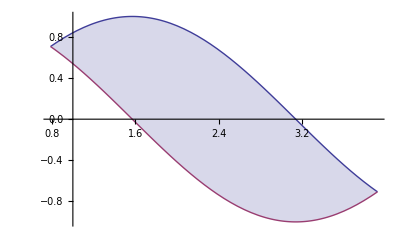

```mathematica
Plot[{f[x],g[x]},{x,a,b},Filling->{1->{2}}]
```

```mathematica
Area=NIntegrate[Abs[f[x]-g[x]],{x,a,b}]
```

2.82843